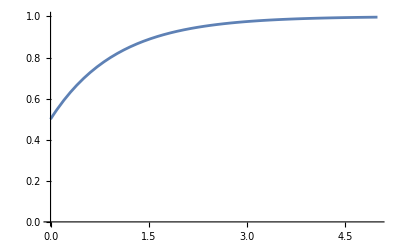

```mathematica
Plot[1-(1-r0)Exp[-t/τ] /. {r0->0.5,τ->1},{t,0,5},PlotRange->{0,1}]
```

```mathematica
Solve[1-(1-r0)Exp[-t]==1/2 ,t,Assumptions->{t∈Reals,0<=r0<=1}]
```

{{t→Log[-2 (-1+r0)]}}

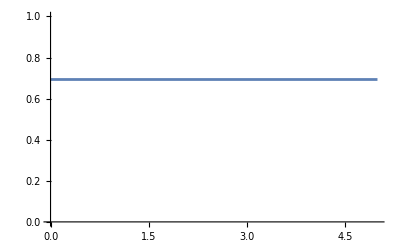

```mathematica
Plot[Log[2-2 r0] /. {r0->0,τ->1},{t,0,5},PlotRange->{0,1}]
```

```mathematica
FullSimplify[Log[-2 (-1+r0)]]
```

Log[2-2 r0]

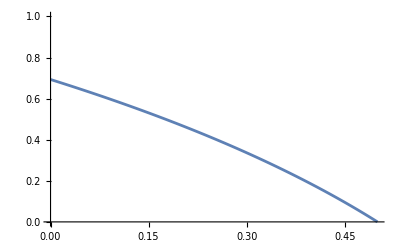

```mathematica
Plot[{Log[2-2 r0]},{r0,0,1/2},PlotRange->{0,1}]
```